# Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\quantum_chaotic_channels\MG files\Sweep hz

```mathematica
Get["D:\\quantum_chaotic_channels\\Mathematica_packages\\QMB.wl"]
```

```mathematica
KroneckerVectorProduct[a_,b_]:=Flatten[KroneckerProduct[a,b]];
BlochVector[ρ_]:=Tr[Pauli[#].ρ]&/@Range[3];
Parity[ψ_,L_]:=ψ[[FromDigits[Reverse[#],2]+1&/@Tuples[{0,1},L]]];
Braket[a_,b_]:=Conjugate[a].b;
MeanLevelSpacingRatio[eigenvalues_]:=Mean[Min/@Transpose[{#,1/#}]&[Ratios[Differences[eigenvalues]]]];
Clear[SurvivalProbability];
SurvivalProbability[ψt_,ψ0_]:=Abs[Braket[ψ0,ψt]]^2;
ClearAll[Superoperator](*nuevo*)
Superoperator[t_,ψ0E_,eigVals_,eigVecs_,L_]:=
	Module[{ψf,ρfSE(*SE final state*)},
		ψf=StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[#],ψ0E],eigVals,eigVecs]&/@{{0},{1}};
		ρfSE=Dyad[ψf[[#1]],ψf[[#2]]]&@@@Tuples[{1,2},2];
		Transpose[Flatten[MatrixPartialTrace[#,2,{2,2^(L-1)}]]&/@ρfSE]
];
```

```mathematica
Clear[bloch];
bloch[rho_]:={2Re[rho[[1,2]]],-2Im[rho[[1,2]]],rho[[1,1]]-rho[[2,2]]};
(*Plot Bloch sphere with Bloch vector*)
plotsphere=SphericalPlot3D[1,{theta,0,Pi},{phi,0,2 Pi},PlotStyle->Opacity[0.07],PlotRange->{{-1,1},{-1,1},{-1,1}},Boxed->False,Axes->False];
plotsphere2=Graphics3D[{Opacity[0.3],Sphere[{0,0,0},1]}];
Clear[rho];
rho[vec_]:={{vec[[1]],vec[[2]]},{vec[[3]],vec[[4]]}};
```

```mathematica
LaunchKernels[16]
```

{Local (16),Local (16),Local (16),Local (16),Local (16),Local (16),Local (16),Local (16),Local (16),Local (16),Local (16),Local (16),Local (16),Local (16),Local (16),Local (16)}

# Sweep of h_z

## LDoS

## Hamiltonian

```mathematica
(*Set parameters in integrable region and compute Hamiltonian, and its eigenvalues and eigenvectors*)
L=5(*number of spins*);
{hx,hz,J}={1,1.5,ConstantArray[1,L-1]};
```

{0.588219,0.48745}

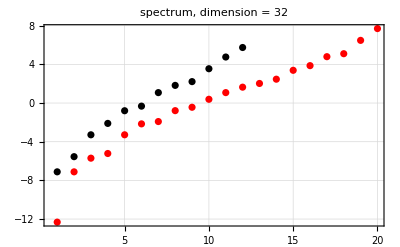

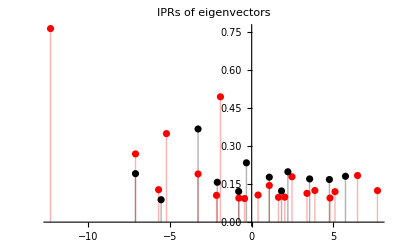

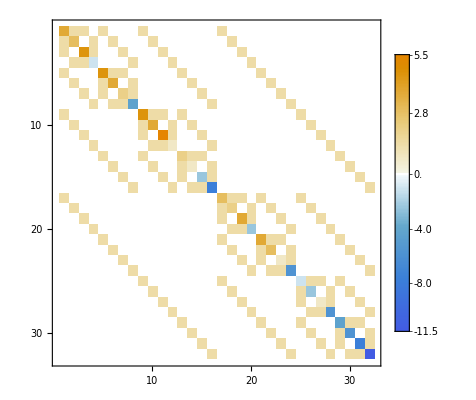

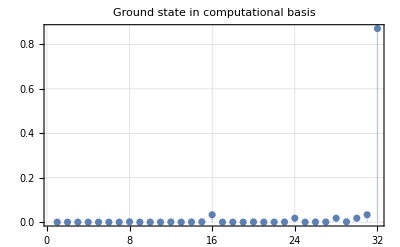

```mathematica
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigVals,eigVecs}=Transpose[Sort[Transpose[Eigensystem[H]]]];
{EvenEigVals,evenEigenVecs}={eigVals[[#]],eigVecs[[#]]}&[Flatten[Position[Round[ParallelMap[Braket[#,Parity[#,L]]&,eigVecs],10.^0],1.]]];
OddEigVals=Complement[eigVals,EvenEigVals];
OddEigVecs=Complement[eigVecs,evenEigenVecs];
{MeanLevelSpacingRatio[OddEigVals],MeanLevelSpacingRatio[EvenEigVals]}
ListPlot[{EvenEigVals,OddEigVals},PlotRange->All,PlotTheme->"Detailed",PlotStyle->{Red,Black},ImageSize->400,PlotLabel->Style["spectrum, dimension = "<>ToString[2^L],25,Black]]
iprM=ParallelTable[Total[Quiet[Abs[i]^4]],{i,evenEigenVecs}];
iprm=ParallelTable[Total[Quiet[Abs[i]^4]],{i,OddEigVecs}];
ListPlot[{Transpose[{EvenEigVals,iprM}],Transpose[{OddEigVals,iprm}]},PlotRange->All,Filling->Axis,ImageSize->400,PlotStyle->{Red,Black},PlotLabel->Style["IPRs of eigenvectors",25,Black]]
MatrixPlot[H,PlotRange->All,PlotTheme->"Detailed"]
ListPlot[Abs[eigVecs[[1]]]^2,PlotRange->All,Filling->Axis,PlotTheme->"Detailed",ImageSize->400,PlotLabel->Style["Ground state in computational basis",25,Black]]
```

## Initial state all random

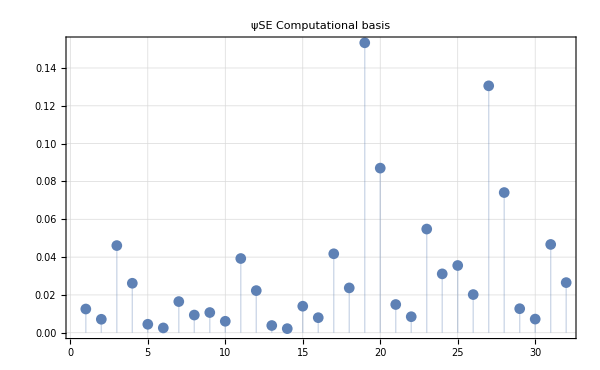
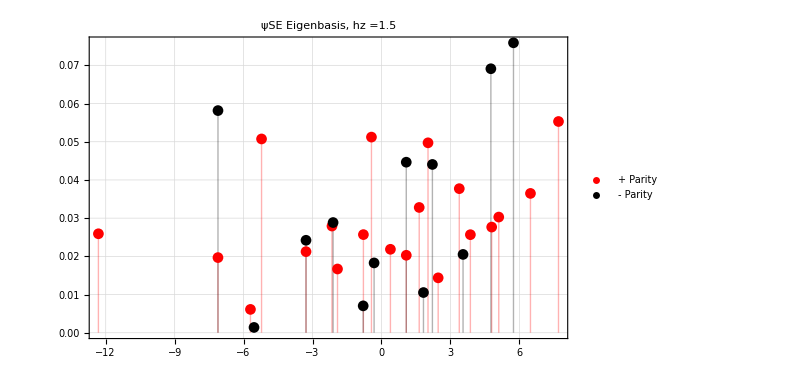

```mathematica
ψ0E=RandomChainProductState[L];
ψ0Espineven=Conjugate[evenEigenVecs].ψ0E;
ψ0Espinodd=Conjugate[OddEigVecs].ψ0E;
plota=ListPlot[Abs[ψ0E]^2,PlotRange->All,Filling->Axis,PlotTheme->"Detailed",ImageSize->600,PlotLabel->Style["ψSE Computational basis",25,Black]];
plotb=ListPlot[{Transpose[{EvenEigVals,Abs[ψ0Espineven]^2}],Transpose[{OddEigVals,Abs[ψ0Espinodd]^2}]},PlotRange->All,Filling->Axis,PlotTheme->"Detailed",ImageSize->600,PlotLabel->Style["ψSE Eigenbasis, hz ="<>ToString[hz],25,Black],PlotStyle->{Red,Black},PlotLegends->{Style["+ Parity",20,Red],Style["- Parity",20,Black]}];
Row[{plota,plotb}]
```

## Initial state coherent state

```mathematica
Clear[ψ0SE];
a=RandomReal[];
state=qubit[a,a];
ψ0SE=coherentstate[state,L];
a
```

0.882194

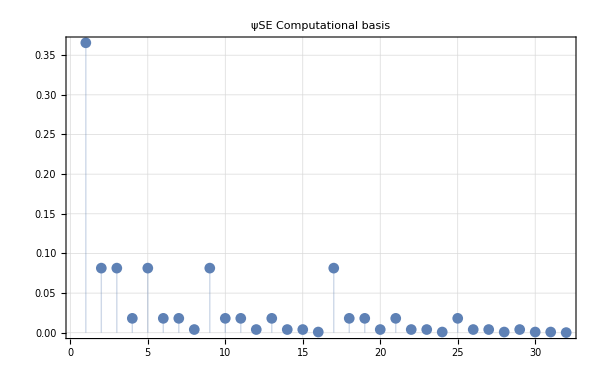
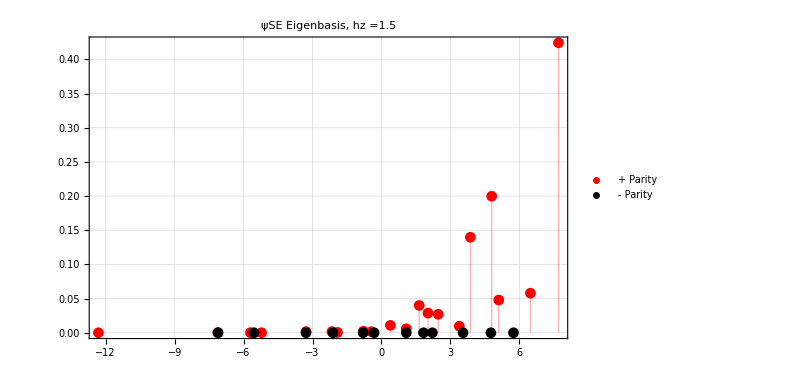

```mathematica
ψ0Espineven=Conjugate[evenEigenVecs].ψ0SE;
ψ0Espinodd=Conjugate[OddEigVecs].ψ0SE;
plota=ListPlot[Abs[ψ0SE]^2,PlotRange->All,Filling->Axis,PlotTheme->"Detailed",ImageSize->600,PlotLabel->Style["ψSE Computational basis",25,Black]];
plotb=ListPlot[{Transpose[{EvenEigVals,Abs[ψ0Espineven]^2}],Transpose[{OddEigVals,Abs[ψ0Espinodd]^2}]},PlotRange->All,Filling->Axis,PlotTheme->"Detailed",ImageSize->600,PlotLabel->Style["ψSE Eigenbasis, hz ="<>ToString[hz],25,Black],PlotStyle->{Red,Black},PlotLegends->{Style["+ Parity",20,Red],Style["- Parity",20,Black]}];
Row[{plota,plotb}]
```

```mathematica
Clear[ψ0SE];
state=qubit[Pi/4,Pi/4];
ψ0SE=coherentstate[state,L];
```

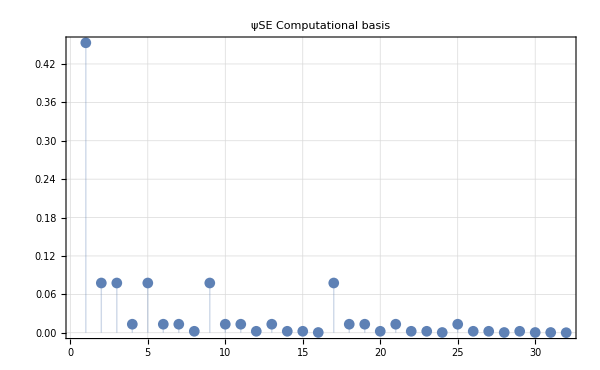
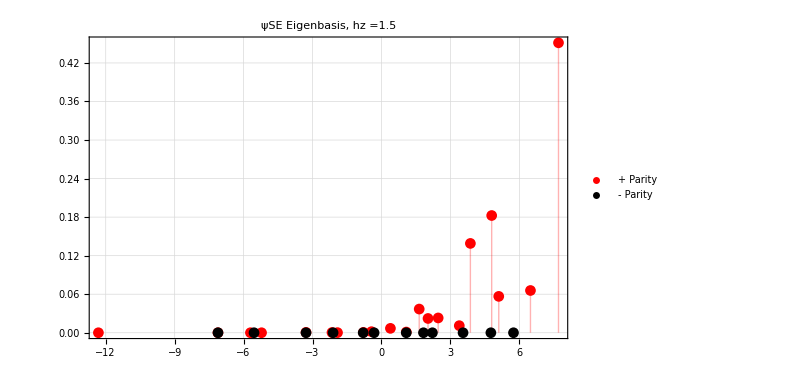

```mathematica
ψ0Espineven=Conjugate[evenEigenVecs].ψ0SE;
ψ0Espinodd=Conjugate[OddEigVecs].ψ0SE;
plota=ListPlot[Abs[ψ0SE]^2,PlotRange->All,Filling->Axis,PlotTheme->"Detailed",ImageSize->600,PlotLabel->Style["ψSE Computational basis",25,Black]];
plotb=ListPlot[{Transpose[{EvenEigVals,Abs[ψ0Espineven]^2}],Transpose[{OddEigVals,Abs[ψ0Espinodd]^2}]},PlotRange->All,Filling->Axis,PlotTheme->"Detailed",ImageSize->600,PlotLabel->Style["ψSE Eigenbasis, hz ="<>ToString[hz],25,Black],PlotStyle->{Red,Black},PlotLegends->{Style["+ Parity",20,Red],Style["- Parity",20,Black]}];
Row[{plota,plotb}]
```

## 0<=t<=5

```mathematica
ψT={coherentstate[qubit[RandomReal[],RandomReal[]],L-1],VectorFromKetInComputationalBasis[ConstantArray[1,L-1]],RandomChainProductState[L-1]};
```

```mathematica
styles={Style["Coherent state, h_z = "<>ToString[hz],50,Black],Style["Up state, h_z = "<>ToString[hz],50,Black],Style["Random product state, h_z = "<>ToString[hz],50,Black]};
```

```mathematica
tf=5.0;
```

```mathematica
(*For each initial state compute bloch sphere dynamics and export it as video*)
figs={};
listplots={};
Do[
AppendTo[figs,{}];
choiEigenvalues={};
Do[
superOp=Superoperator[t,ψT[[i]],eigVals,eigVecs,L];
f[x_,y_,z_]:=BlochVector[ArrayReshape[superOp.{1+z,x-ⅈ y,x+ⅈ y,1-z}/2,{2,2}]];
AppendTo[figs[[i]],
Graphics3D[{{Opacity[0.2],Sphere[]},
{Arrow[{{0,0,0},{0,0,1}}],Arrow[{{0,0,0},{0,1,0}}],Arrow[{{0,0,0},{1,0,0}}]},
Opacity[0.75],GrayLevel[.4],
Flatten[Table[Point[f@@{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}],{θ,0,Pi,Pi/30},{ϕ,0,2Pi,Pi/30}]],
{Red,PointSize[0.03],Point[f@@{0,0,1}]},
{Green,PointSize[0.03],Point[f@@{0,0,-1}]},
{Orange,PointSize[0.03],Point[f@@{0,1,0}]},
{Cyan,PointSize[0.03],Point[f@@{0,-1,0}]},
{Magenta,PointSize[0.03],Point[f@@{1,0,0}]},
{Blue,PointSize[0.03],Point[f@@{-1,0,0}]}
},
PlotLabel->"t = "<>ToString[t],
Axes->True,Ticks->None,AxesLabel->{x,y,z},
LabelStyle->Directive[Black,FontSize->22,FontFamily->"Arial"],
ViewPoint->{Pi,Pi/2,2},ImageSize->800
]
];
AppendTo[choiEigenvalues,
Transpose[{ConstantArray[t,4],Eigenvalues[1/2.Reshuffle[superOp]]}]
];,{t,0,tf,.1}];
AppendTo[listplots,
ListPlot[Transpose[Chop[choiEigenvalues]],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Dashed],
PlotMarkers->{Automatic,Scaled[0.03]},
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->20],
FrameLabel->{"StyleBox[\"t\",FontSlant->\"Italic\"]","eigenvalues( Choi )"},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->800,PlotLabel->styles[[i]]]];
,{i,3}]
```

```mathematica
t=0.2;
Grid[Table[{Show[listplots[[i]],Epilog->{Red,Line[{{t,-1},{t,2}}]}],figs[[i,Round[t*10]+1]]},{i,3}],Spacings->{5,5},Alignment->{Center,Center},Frame->All]
```

```mathematica
grids=Table[Grid[Table[{Show[listplots[[i]],Epilog->{Red,Line[{{t,-1},{t,2}}]}],figs[[i,Round[t*10]+1]]},{i,3}],Spacings->{5,5},Alignment->{Center,Center},Frame->All],{t,0,tf,0.1}];
```

```mathematica
Table[Export["h_z_"<>ToString[hz]<>"_frame_"<>ToString[i]<>".png",grids[[i]],ImageSize->1000,ImageResolution->300],{i,3}]
```

{h_z_1.5_frame_1.png,h_z_1.5_frame_2.png,h_z_1.5_frame_3.png}

## Full sweep

```mathematica
hzlist=Range[1.5,3,0.1];
```

```mathematica
Do[
styles={Style["Coherent state, h_z = "<>ToString[hz],50,Black],Style["Up state, h_z = "<>ToString[hz],50,Black],Style["Random product state, h_z = "<>ToString[hz],50,Black]};
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigVals,eigVecs}=Transpose[Sort[Transpose[Eigensystem[H]]]];

figs={};
listplots={};
Do[
AppendTo[figs,{}];
choiEigenvalues={};
Do[
superOp=Superoperator[t,ψT[[i]],eigVals,eigVecs,L];
f[x_,y_,z_]:=BlochVector[ArrayReshape[superOp.{1+z,x-ⅈ y,x+ⅈ y,1-z}/2,{2,2}]];
AppendTo[figs[[i]],
Graphics3D[{{Opacity[0.2],Sphere[]},
{Arrow[{{0,0,0},{0,0,1}}],Arrow[{{0,0,0},{0,1,0}}],Arrow[{{0,0,0},{1,0,0}}]},
Opacity[0.75],GrayLevel[.4],
Flatten[Table[Point[f@@{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}],{θ,0,Pi,Pi/30},{ϕ,0,2Pi,Pi/30}]],
{Red,PointSize[0.03],Point[f@@{0,0,1}]},
{Green,PointSize[0.03],Point[f@@{0,0,-1}]},
{Orange,PointSize[0.03],Point[f@@{0,1,0}]},
{Cyan,PointSize[0.03],Point[f@@{0,-1,0}]},
{Magenta,PointSize[0.03],Point[f@@{1,0,0}]},
{Blue,PointSize[0.03],Point[f@@{-1,0,0}]}
},
PlotLabel->"t = "<>ToString[t],
Axes->True,Ticks->None,AxesLabel->{x,y,z},
LabelStyle->Directive[Black,FontSize->22,FontFamily->"Arial"],
ViewPoint->{Pi,Pi/2,2},ImageSize->800
]
];
AppendTo[choiEigenvalues,
Transpose[{ConstantArray[t,4],Eigenvalues[1/2.Reshuffle[superOp]]}]
];,{t,0,tf,.1}];
AppendTo[listplots,
ListPlot[Transpose[Chop[choiEigenvalues]],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Dashed],
PlotMarkers->{Automatic,Scaled[0.03]},
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->20],
FrameLabel->{"StyleBox[\"t\",FontSlant->\"Italic\"]","eigenvalues( Choi )"},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->800,PlotLabel->styles[[i]]]];
,{i,3}];



grids=Table[Grid[Table[{Show[listplots[[i]],Epilog->{Red,Line[{{t,-1},{t,2}}]}],figs[[i,Round[t*10]+1]]},{i,3}],Spacings->{5,5},Alignment->{Center,Center},Frame->All],{t,0,tf,0.1}];
Table[Export["h_z_"<>ToString[hz]<>"_frame_"<>ToString[i]<>".png",grids[[i]],ImageSize->1000,ImageResolution->300],{i,Length[grids]}]

,{hz,hzlist}];
```